```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

```mathematica
G2=Interpolation[Import[NotebookDirectory[]<>"points_bG2.m"]];
G2gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_bG2.m"]];
G2gausspoints=Import[NotebookDirectory[]<>"brute_force_points_bG2.m"];
```

```mathematica
δ2=Interpolation[Import[NotebookDirectory[]<>"points_b2.m"]];
δ2gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_b2.m"]];
δ2gausspoints=Import[NotebookDirectory[]<>"brute_force_points_b2.m"];
```

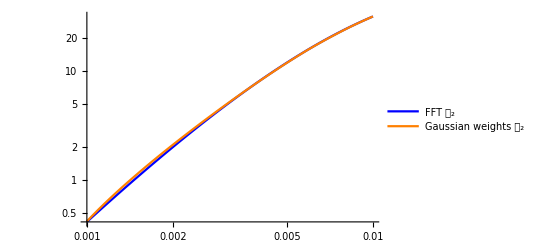

```mathematica
plot1=LogLogPlot[{Re[G2[k]],Re[G2gauss[k]]},{k,0.001,0.01},PlotLegends->{"FFT 𝒢_2","Gaussian weights 𝒢_2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

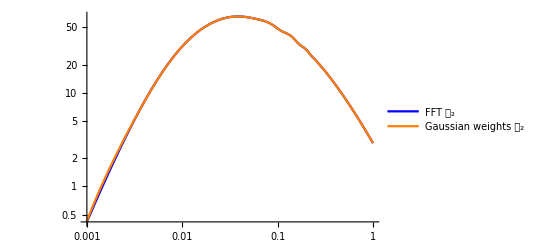

```mathematica
plot1=LogLogPlot[{Re[G2[k]],Re[G2gauss[k]]},{k,0.001,1},PlotLegends->{"FFT 𝒢_2","Gaussian weights 𝒢_2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

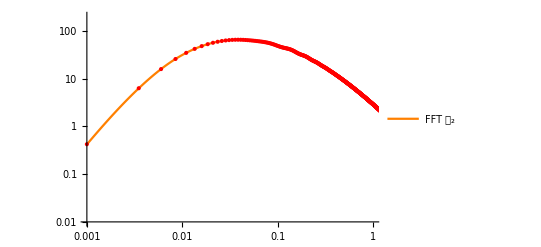

```mathematica
plot1=Show[{LogLogPlot[{Re[G2[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT 𝒢_2"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{0.01,200}},PlotPoints->200],ListLogLogPlot[G2gausspoints//Abs,PlotStyle->{Red}]}]
```

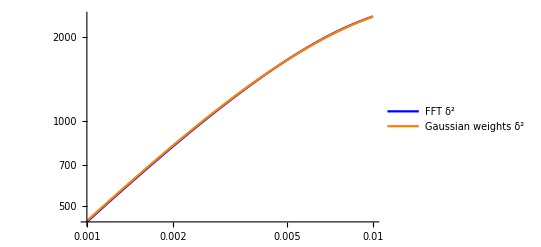

```mathematica
plot2=LogLogPlot[{Re[δ2[k]]//Abs,Re[δ2gauss[k]]//Abs},{k,0.001,0.01},PlotLegends->{"FFT δ^2","Gaussian weights δ^2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

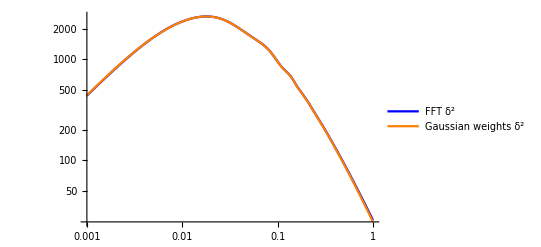

```mathematica
plot2=LogLogPlot[{Re[δ2[k]]//Abs,Re[δ2gauss[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT δ^2","Gaussian weights δ^2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

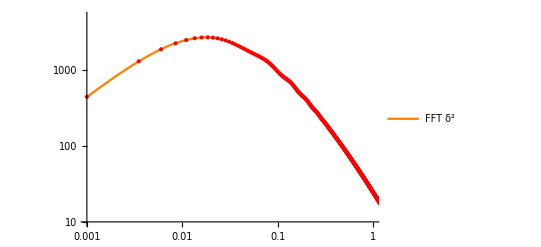

```mathematica
plot2=Show[{LogLogPlot[{Re[δ2[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT δ^2"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{10,5000}},PlotPoints->200],ListLogLogPlot[δ2gausspoints//Abs,PlotStyle->{Red}]}]
```

```mathematica
Export[NotebookDirectory[]<>"comparison_plot_calG2.pdf",plot1];
Export[NotebookDirectory[]<>"comparison_plot_delta_squared.pdf",plot2];
```